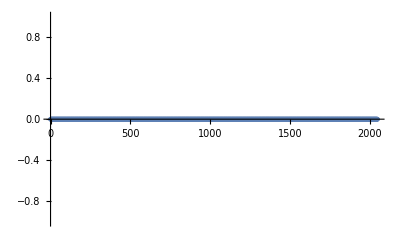

```mathematica
name := "add"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
ListPlot[data]
```

FittedModel[0.]

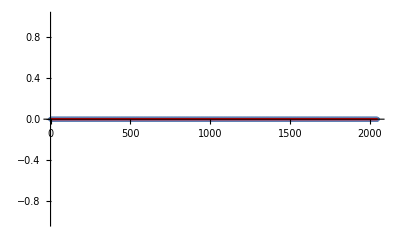

```mathematica
nlm = NonlinearModelFit[data, a*x,{a},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
```